```mathematica
H=ℏ({{0, 1/2 Ωp, 1/2 Ωpp, 0}, {1/2 Ωp, Δp-ⅈ Γ/2, 0, 1/2 Ωs}, {1/2 Ωpp, 0, Δpp-ⅈ Γ/2, 0}, {0, 1/2 Ωs, 0, δ}});ψ=({{c1[t]}, {c2[t]}, {c3[t]}, {c4[t]}});
```

```mathematica
SE=D[ψ, t]==-ⅈ/ℏ H.ψ//FullSimplify
```

{{c1'[t]},{c2'[t]},{c3'[t]},{c4'[t]}}=={{-1/2 ⅈ (Ωp c2[t]+Ωpp c3[t])},{-1/2 ⅈ (Ωp c1[t]+(-ⅈ Γ+2 Δp) c2[t]+Ωs c4[t])},{-1/2 ⅈ (Ωpp c1[t]+(-ⅈ Γ+2 Δpp) c3[t])},{-1/2 ⅈ (Ωs c2[t]+2 δ c4[t])}}

```mathematica
eoms=Table[SE[[All,i,1]],{i,1,4}]
```

{c1'[t]==-1/2 ⅈ (Ωp c2[t]+Ωpp c3[t]),c2'[t]==-1/2 ⅈ (Ωp c1[t]+(-ⅈ Γ+2 Δp) c2[t]+Ωs c4[t]),c3'[t]==-1/2 ⅈ (Ωpp c1[t]+(-ⅈ Γ+2 Δpp) c3[t]),c4'[t]==-1/2 ⅈ (Ωs c2[t]+2 δ c4[t])}

```mathematica
replace1stOrder={c2[t]-> Subscript[c2, 1][t],c4[t]-> Subscript[c4, 1][t],c3[t]-> Subscript[c3, 1][t],c1[t]-> Subscript[c1, 1][t],c1'[t]-> Subscript[c1, 1]'[t],c4'[t]-> Subscript[c4, 1]'[t]}
c31exp=Solve[eoms[[3]]/.{c3'[t]-> 0}/.replace1stOrder,Subscript[c3, 1][t]][[1]]
c21exp=Solve[eoms[[2]]/.{c2'[t]-> 0}/.replace1stOrder,Subscript[c2, 1][t]][[1]]
eom11=eoms[[1]]/.replace1stOrder/.c21exp/.c31exp//FullSimplify
eom41=eoms[[4]]/.replace1stOrder/.c21exp//FullSimplify
```

{c2[t]→c2_1[t],c4[t]→c4_1[t],c3[t]→c3_1[t],c1[t]→c1_1[t],c1'[t]→c1_1'[t],c4'[t]→c4_1'[t]}

{c3_1[t]→-(ⅈ Ωpp c1_1[t])/(Γ+2 ⅈ Δpp)}

{c2_1[t]→-(ⅈ (Ωp c1_1[t]+Ωs c4_1[t]))/(Γ+2 ⅈ Δp)}

(Ωpp^2 c1_1[t])/(2 Γ+4 ⅈ Δpp)+(Ωp (Ωp c1_1[t]+Ωs c4_1[t]))/(2 (Γ+2 ⅈ Δp))+c1_1'[t]==0

(Ωs (Ωp c1_1[t]+Ωs c4_1[t]))/(Γ+2 ⅈ Δp)+2 (ⅈ δ c4_1[t]+c4_1'[t])==0

```mathematica
Solve[eom41,Subscript[c4, 1]'[t]]
```

```mathematica
eom41d={{Subscript[c4, 1]'[t]->1/2 (-2 ⅈ δ Subscript[c4, 1][t]-(Ωs (Ωp Subscript[c1, 1][t]+Ωs Subscript[c4, 1][t]))/(Γ+2 ⅈ Δp))}}[[1]]
```

{c4_1'[t]→1/2 (-2 ⅈ δ c4_1[t]-(Ωs (Ωp c1_1[t]+Ωs c4_1[t]))/(Γ+2 ⅈ Δp))}

```mathematica
D[eom11,t]
```

(Ωpp^2 c1_1'[t])/(2 Γ+4 ⅈ Δpp)+(Ωp (Ωp c1_1'[t]+Ωs c4_1'[t]))/(2 (Γ+2 ⅈ Δp))+c1_1''[t]==0

```mathematica
sol1order1=DSolve[{(Ωpp^2 Subscript[c1, 1][t])/(2 Γ+4 ⅈ Δpp)+(Ωp (Ωp Subscript[c1, 1][t]+Ωs Subscript[c4, 1][t]))/(2 (Γ+2 ⅈ Δp))+Subscript[c1, 1]'[t]==0,(Ωs (Ωp Subscript[c1, 1][t]+Ωs Subscript[c4, 1][t]))/(Γ+2 ⅈ Δp)+2 (ⅈ δ Subscript[c4, 1][t]+Subscript[c4, 1]'[t])==0,Subscript[c1, 1][0]==1,Subscript[c4, 1][0]==0},{Subscript[c4, 1][t],Subscript[c1, 1][t]},t][[1]];
```

```mathematica
Subscript[pop4, 1][t_]=(Subscript[c4, 1][t]Subscript[c4, 1][t]*/.sol1order1//ComplexExpand)
```

(ⅇ^(2 (1-1) (1)11) Γ^2 Ωp^2 1 1^2 Cos[1]^2)/(√((1)^2+(16 Γ^2 δ Δp Ωp^2+13)^2))+30+(4 5 1^2)/(√(((11)^2+1))
 |  |  |  |

```mathematica
MHz=10^6;GHz=10^9;μs=10^-6;
pip4[t_]=Subscript[pop4, 1][t]/.{Ωp-> 2π 15 MHz,Ωpp-> 2π  15 √12 MHz,Ωs-> 250 2π MHz,Γ-> 2π 100 MHz,Δp-> 2π 21 GHz,Δpp-> 2π 25 GHz,δ-> 0}//N
```

0.00384527 2.71828^(-676.074 t) Cos[169014. t]^2-0.00769054 2.71828^(-11510.2 t) Cos[169014. t] Cos[4.69242×10^6 t]+0.00384527 2.71828^(-22344.4 t) Cos[4.69242×10^6 t]^2+0.00384527 2.71828^(-676.074 t) Sin[169014. t]^2-0.00769054 2.71828^(-11510.2 t) Sin[169014. t] Sin[4.69242×10^6 t]+0.00384527 2.71828^(-22344.4 t) Sin[4.69242×10^6 t]^2

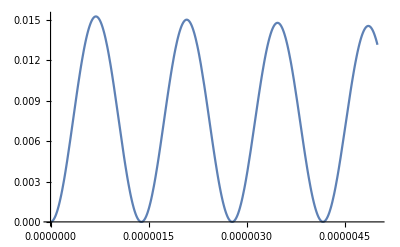

```mathematica
Plot[pip4[t],{t,0,5 μs}]
```